```mathematica
Functions
```

```mathematica
PDeath[day_,accept_,endp_]:=Module[{a,b,p},
a=accept[[;;,day,2]]/Total[accept[[;;,day,2]]];
(*Probability that outbreak has died out*)
b=endp[[;;,day,2]];
p=Total[a*b];
Return[p];
];

FindMeanSize[s_,val_]:=Module[{ss,m},
ss=s[[val]];
m=Total[Table[ss[[i,1]]*ss[[i,2]],{i,1,Length[ss]}]];
Return[m];
];

fourParamChartStyle={RGBColor["#4477AA"],RGBColor["#117733"],RGBColor["#DDCC77"],RGBColor["#CC6677"]};
```

```mathematica
SetDirectory["/Users/chris/Documents/H1N2/Code/Results_HPC/"];
p=0.04;
times=Flatten[Import["Faster/P"<>ToString[p]<>"/Data/Time_points.dat","Table"]];
accept4=Table[Import["Faster/P"<>ToString[p]<>"/Acceptance_rate"<>ToString[i]<>".dat"],{i,1,40}];
sizedist4=Table[Import["Faster/P"<>ToString[p]<>"/Sizes_time_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
origdist4=Table[Import["Faster/P"<>ToString[p]<>"/Origin_stats_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
For[i=1,i<=Length[origdist4],i++,
origdist4[[i,;;,1]]=-origdist4[[i,;;,1]];
];
pend4=Import["Faster/P"<>ToString[p]<>"/P_Outbreak_End.dat","Table"];

p=0.06;
accept6=Table[Import["Faster/P"<>ToString[p]<>"/Acceptance_rate"<>ToString[i]<>".dat"],{i,1,40}];
sizedist6=Table[Import["Faster/P"<>ToString[p]<>"/Sizes_time_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
origdist6=Table[Import["Faster/P"<>ToString[p]<>"/Origin_stats_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
For[i=1,i<=Length[origdist6],i++,
origdist6[[i,;;,1]]=-origdist6[[i,;;,1]];
];
pend6=Import["Faster/P"<>ToString[p]<>"/P_Outbreak_End.dat","Table"];

p=0.08;
accept8=Table[Import["Faster/P"<>ToString[p]<>"/Acceptance_rate"<>ToString[i]<>".dat"],{i,1,40}];
sizedist8=Table[Import["Faster/P"<>ToString[p]<>"/Sizes_time_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
origdist8=Table[Import["Faster/P"<>ToString[p]<>"/Origin_stats_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
For[i=1,i<=Length[origdist8],i++,
origdist8[[i,;;,1]]=-origdist8[[i,;;,1]];
];
pend8=Import["Faster/P"<>ToString[p]<>"/P_Outbreak_End.dat","Table"];

p=0.1;
accept10=Table[Import["Faster/P"<>ToString[p]<>"/Acceptance_rate"<>ToString[i]<>".dat"],{i,1,40}];
sizedist10=Table[Import["Faster/P"<>ToString[p]<>"/Sizes_time_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
origdist10=Table[Import["Faster/P"<>ToString[p]<>"/Origin_stats_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
For[i=1,i<=Length[origdist10],i++,
origdist10[[i,;;,1]]=-origdist10[[i,;;,1]];
];
pend10=Import["Faster/P"<>ToString[p]<>"/P_Outbreak_End.dat","Table"];
```

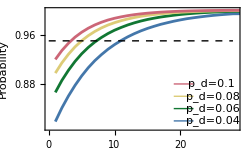

```mathematica
Show[ListLinePlot[{pend4,pend6,pend8,pend10},PlotRange->{{0,28.5},All},Frame->True,PlotStyle->fourParamChartStyle,FrameLabel->{{"Probability",None},{"Days after initial detection","Estimated probability outbreak has ended"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Graphics[{fourParamChartStyle[[4]],Line[{{19,0.88},{22,0.88}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{19,0.86},{22,0.86}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{19,0.84},{22,0.84}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{19,0.82},{22,0.82}}]}],Graphics[Text["p_d=0.1",{24.7,0.88}]],Graphics[Text["p_d=0.08",{25,0.86}]],Graphics[Text["p_d=0.06",{25,0.84}]],Graphics[Text["p_d=0.04",{25,0.82}]],Graphics[{Dashed,Line[{{0,0.95},{28,0.95}}]}]]
```

```mathematica
Population size conditional on not dying out at day 7
```

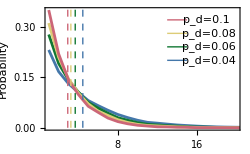

```mathematica
val=7;
s4=sizedist4[[val]];
s6=sizedist6[[val]];
s8=sizedist8[[val]];
s10=sizedist10[[val]];
y1=0.2;
y2=0.24;
y3=0.28;
y4=0.32;
m4=Total[Table[s4[[i,1]]*s4[[i,2]],{i,1,Length[s4]}]];
m6=Total[Table[s6[[i,1]]*s6[[i,2]],{i,1,Length[s6]}]];
m8=Total[Table[s8[[i,1]]*s8[[i,2]],{i,1,Length[s8]}]];
m10=Total[Table[s10[[i,1]]*s10[[i,2]],{i,1,Length[s10]}]];
p1=Show[ListLinePlot[{s4[[2;;]],s6[[2;;]],s8[[2;;]],s10[[2;;]]},PlotRange->{{1,20},All},Frame->True,PlotStyle->fourParamChartStyle,FrameLabel->{{"Probability",None},{"Outbreak size (cases)","Day 7"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Graphics[{fourParamChartStyle[[4]],Line[{{13,y4},{15,y4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{13,y3},{15,y3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{13,y2},{15,y2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{13,y1},{15,y1}}]}],Graphics[Text["p_d=0.1",{17,y4}]],Graphics[Text["p_d=0.08",{17.2,y3}]],Graphics[Text["p_d=0.06",{17.2,y2}]],Graphics[Text["p_d=0.04",{17.2,y1}]],Graphics[{Dashed,fourParamChartStyle[[1]],Line[{{m4,0},{m4,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[2]],Line[{{m6,0},{m6,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[3]],Line[{{m8,0},{m8,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[4]],Line[{{m10,0},{m10,0.5}}]}]]
```

```mathematica
Mean outbreak sizes
```

```mathematica
{m4,m6,m8,m10}
```

{4.45098,3.68372,3.24125,2.92594}

```mathematica
Changes in mean population size conditional on not dying out over time
```

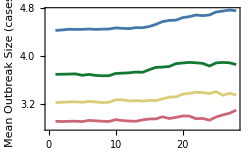

```mathematica
ListLinePlot[{Table[FindMeanSize[sizedist4,i],{i,1,28}],Table[FindMeanSize[sizedist6,i],{i,1,28}],Table[FindMeanSize[sizedist8,i],{i,1,28}],Table[FindMeanSize[sizedist10,i],{i,1,28}]},Frame->True,PlotStyle->fourParamChartStyle,FrameLabel->{{"Mean Outbreak Size (cases)",None},{"Days after detection","Estimates conditional on outbreak surviving"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250]
```

```mathematica
Population size absolute at day 7
```

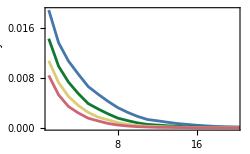

```mathematica
val=7;
s4=sizedist4[[val]];
s6=sizedist6[[val]];
s8=sizedist8[[val]];
s10=sizedist10[[val]];
s4[[;;,2]]=s4[[;;,2]]*(1-pend4[[val,2]]);
s6[[;;,2]]=s6[[;;,2]]*(1-pend6[[val,2]]);
s8[[;;,2]]=s8[[;;,2]]*(1-pend8[[val,2]]);
s10[[;;,2]]=s10[[;;,2]]*(1-pend10[[val,2]]);
s4[[1,2]]=pend4[[val,2]];
s6[[1,2]]=pend6[[val,2]];
s8[[1,2]]=pend8[[val,2]];
s10[[1,2]]=pend10[[val,2]];
(*Mean outbreak sizes*)
m4=Total[Table[s4[[i,1]]*s4[[i,2]],{i,1,Length[s4]}]];
m6=Total[Table[s6[[i,1]]*s6[[i,2]],{i,1,Length[s6]}]];
m8=Total[Table[s8[[i,1]]*s8[[i,2]],{i,1,Length[s8]}]];
m10=Total[Table[s10[[i,1]]*s10[[i,2]],{i,1,Length[s10]}]];
p1=Show[ListLinePlot[{s4[[2;;]],s6[[2;;]],s8[[2;;]],s10[[2;;]]},PlotRange->{{1,20},All},Frame->True,PlotStyle->fourParamChartStyle,FrameLabel->{{"Probability",None},{"Outbreak size (cases)","Day 7"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250]]
```

```mathematica
Mean outbreak sizes
```

```mathematica
{m4,m6,m8,m10}
```

{0.365853,0.191222,0.112604,0.0706672}

```mathematica
Time of spillover event
```

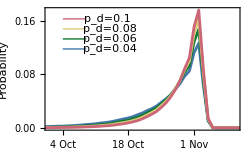

```mathematica
val=29;
y1=0.118;
dy=0.015;
y2=y1+dy;
y3=y2+dy;
y4=y3+dy;
x1=-51;
dx=5;
x2=-41;
Show[ListLinePlot[{origdist4[[val]],origdist6[[val]],origdist8[[val]],origdist10[[val]]},PlotRange->{{-54,-14},All},Frame->True,Axes->False,PlotStyle->fourParamChartStyle,FrameLabel->{{"Probability",None},{"Date","Time of spillover event"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250,FrameTicks->{{Automatic,Automatic},{{{-23-28,"4 Oct"},{-23-21,"11 Oct"},{-23-14,"18 Oct"},{-23-7,"25 Oct"},{-23,"1 Nov"},{-23+7,"8 Nov"}},Automatic}}],Graphics[{fourParamChartStyle[[4]],Line[{{x1,y4},{x1+dx,y4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{x1,y3},{x1+dx,y3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{x1,y2},{x1+dx,y2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{x1,y1},{x1+dx,y1}}]}],Graphics[Text["p_d=0.1",{x2-0.5,y4}]],Graphics[Text["p_d=0.08",{x2,y3}]],Graphics[Text["p_d=0.06",{x2,y2}]],Graphics[Text["p_d=0.04",{x2,y1}]]]
```

```mathematica
Maximum likelihood times relative to first observation
```

```mathematica
Sort[origdist4[[val]],#1[[2]]>#2[[2]]&][[1,1]]
Sort[origdist6[[val]],#1[[2]]>#2[[2]]&][[1,1]]
Sort[origdist8[[val]],#1[[2]]>#2[[2]]&][[1,1]]
Sort[origdist10[[val]],#1[[2]]>#2[[2]]&][[1,1]]
```

-22

-22

-22

«1 more identical outputs»

```mathematica
Mean times relative to first observation
```

```mathematica
Total[Table[origdist4[[val,i,1]]*origdist4[[val,i,2]],{i,1,Length[origdist4[[val]]]}]]
Total[Table[origdist6[[val,i,1]]*origdist6[[val,i,2]],{i,1,Length[origdist6[[val]]]}]]
Total[Table[origdist8[[val,i,1]]*origdist8[[val,i,2]],{i,1,Length[origdist8[[val]]]}]]
Total[Table[origdist10[[val,i,1]]*origdist10[[val,i,2]],{i,1,Length[origdist10[[val]]]}]]
```

-28.3808

-27.0574

-26.2619

-25.7173

```mathematica
Final distribution of R0
```

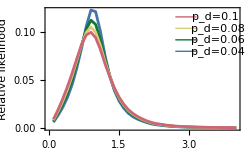

```mathematica
a4=accept4[[;;,-1,2]]/Total[accept4[[;;,-1,2]]];
ca4=a4;
For[i=2,i<=Length[ca4],i++,
ca4[[i]]=ca4[[i]]+ca4[[i-1]];
];
ca4=Partition[Riffle[Table[0.1*i,{i,1,40}],ca4],2];
a4=Partition[Riffle[Table[0.1*i,{i,1,40}],a4],2];

a6=accept6[[;;,-1,2]]/Total[accept6[[;;,-1,2]]];
ca6=a6;
For[i=2,i<=Length[ca6],i++,
ca6[[i]]=ca6[[i]]+ca6[[i-1]];
];
ca6=Partition[Riffle[Table[0.1*i,{i,1,40}],ca6],2];
a6=Partition[Riffle[Table[0.1*i,{i,1,40}],a6],2];

a8=accept8[[;;,-1,2]]/Total[accept8[[;;,-1,2]]];
ca8=a8;
For[i=2,i<=Length[ca8],i++,
ca8[[i]]=ca8[[i]]+ca8[[i-1]];
];
ca8=Partition[Riffle[Table[0.1*i,{i,1,40}],ca8],2];
a8=Partition[Riffle[Table[0.1*i,{i,1,40}],a8],2];

a10=accept10[[;;,-1,2]]/Total[accept10[[;;,-1,2]]];
ca10=a10;
For[i=2,i<=Length[ca10],i++,
ca10[[i]]=ca10[[i]]+ca10[[i-1]];
];
ca10=Partition[Riffle[Table[0.1*i,{i,1,40}],ca10],2];
a10=Partition[Riffle[Table[0.1*i,{i,1,40}],a10],2];

y1=0.08;
dy=0.012;
y2=y1+dy;
y3=y2+dy;
y4=y3+dy;
x1=2.7;
dx=0.45;
x2=3.6;
Show[ListLinePlot[{a4,a6,a8,a10},Frame->True,Axes->False,PlotStyle->fourParamChartStyle,FrameLabel->{"R_0","Relative likelihood"},FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Graphics[{fourParamChartStyle[[4]],Line[{{x1,y4},{x1+dx,y4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{x1,y3},{x1+dx,y3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{x1,y2},{x1+dx,y2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{x1,y1},{x1+dx,y1}}]}],Graphics[Text["p_d=0.1",{x2-0.05,y4}]],Graphics[Text["p_d=0.08",{x2,y3}]],Graphics[Text["p_d=0.06",{x2,y2}]],Graphics[Text["p_d=0.04",{x2,y1}]]]
```

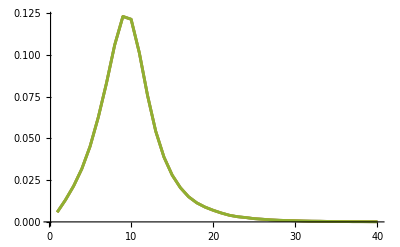

```mathematica
ListLinePlot[{accept4[[;;,1,2]]/Total[accept4[[;;,1,2]]],accept4[[;;,5,2]]/Total[accept4[[;;,5,2]]],accept4[[;;,10,2]]/Total[accept4[[;;,10,2]]]},PlotRange->All]
```